## Initial setup

Some of the options below may need to be changed as necessary.

```mathematica
Needs["AutomaticUnits`"];
Needs["LevelScheme`"];
Needs["Cosmology`"];
```

```mathematica
SetDirectory["~/myWork/np_sandbox/005"];
```

## Read in files

Define a simple function to read in a file, and extract columns 1-3

```mathematica
readFile[fn_] := (Part[#,{1,4,5}] &) /@ Import[fn, "Table"];
```

```mathematica
dr7 = readFile["DR7.txt"];
dr9 = readFile["DR9.txt"];
```

```mathematica
dr7[[1]]
```

{2.50646,7.74611,0.0490665}

## Make first cut at plot

```mathematica
SetOptions[Figure, ImageSize-> 72*{18,12}];
```

```mathematica
cvt[data_, scal_, disp_:0] := Module[{r, xi, err},
r = data[[1]]; xi = data[[2]]; err= data[[3]];
{r/scal, ErrorValue[xi*r^2-disp, err*r^2]}
];
```

```mathematica
dr7dV = 1356.0*0.702; 
dr9dV = 2094.0*0.7;
```

```mathematica
fig = Figure[{
SetOptions[FigurePanel, FontFamily-> "Times", FontSize-> 35],
SetOptions[SchemeArrow, FontFamily-> "Times", FontSize->35],
FigurePanel[
{{0,1},{0,1}},
Frame->True,
PlotRange-> {{0.0,0.15}, {-100,150}},
FrameTicks->{LinTicks[0.0, 0.15], 
                         None, 
                         LinTicks[0.0, 0.15], 
		       None},
ExtendRange-> 0.05, 
TickNudge->{{0,-3},{-3,0},0,0},
LabB->"Galaxy Separation/Distance to Galaxies",BufferB->4.0,
LabL->"Scaled Correlation Function", BufferL->5.0
],
SetOptions[DataLine, ShowLine->False],
SetOptions[DataSymbol, SymbolSize-> 10],
DataPlot[(cvt[#,dr7dV] &) /@ dr7, DataSymbol->{SymbolShape-> "Circle", FillColor-> Red, Thickness->2}],
DataPlot[(cvt[#,dr9dV,70] &) /@ dr9, DataSymbol->{SymbolShape-> "Square", FillColor-> Blue, Thickness->2}],
SchemeArrow[{0.08, 120}, {0.105, 110}, Thickness->3, 
LabT->"BAO at z=0.35"],
SchemeArrow[{0.05, 10}, {0.07, 0}, Thickness->3, 
LabT->"BAO at z=0.57"],
},
PlotRange->{{-0.2,1.1},{-0.2,1.1}},
Frame-> False ] ;
Export["dr79.pdf", fig];
```

## Lookback time stuff

Pick a cosmology

```mathematica
FoMSWG
```

{Omegabh2→0.0227,OmegaMh2→0.1326,OmegaKh2→0.,OmegaDEh2→0.3844,ns→0.963,w0→-1.,wa→0.,TCMB→2.726,gamma→0.55}

Hubble time in billions of years

```mathematica
th0 =(#&) @@Convert[HubbleTime, Year]/1*^9
```

9.78461942314

```mathematica
alist = 10^Table[x, {x,-3.0,0.1 , 0.01}];
```

```mathematica
tlist =({-tlookback[#, FoMSWG]*th0, #} &) /@ alist;
```

```mathematica
tlist[[1]]
```

{-13.6995,0.001}

```mathematica
tDR7 = -tlookback[z2a[0.35], FoMSWG]*th0;
tDR9 = -tlookback[z2a[0.57], FoMSWG]* th0;
```

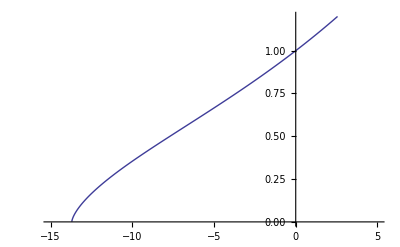

```mathematica
ListLinePlot[tlist, PlotRange->{{-15, 5},{0,1.2}}]
```

## Make Animated Version

```mathematica
avals = Join[Range[0.85, 1.15, 0.01],Range[1.14, 1.0, -0.01]]
```

{0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.14,1.13,1.12,1.11,1.1,1.09,1.08,1.07,1.06,1.05,1.04,1.03,1.02,1.01,1.}

```mathematica
fig2 = Table[Figure[{
(* Overall options *)
SetOptions[FigurePanel, FontFamily-> "Times", FontSize-> 35],
SetOptions[SchemeArrow, FontFamily-> "Times", FontSize->35],

(* Main figure panel *)
FigurePanel[
{{0,1},{0,1}},
Frame->True,
PlotRange-> {{50.0,250.0}, {-100,150}},
FrameTicks->{LinTicks[0.0, 250], 
                         None, 
                         LinTicks[0.0, 250], 
		       None},
ExtendRange-> 0.05, 
TickNudge->{{0,-3},{-3,0},0,0},
LabB->"Galaxy Separation (Mpc)",BufferB->4.0,
LabL->"Scaled Correlation Function", BufferL->5.0
],

(* Plot data *)
SetOptions[DataLine, ShowLine->False],
SetOptions[DataSymbol, SymbolSize-> 10],
DataPlot[(cvt[#,0.702*a] &) /@ dr7, DataSymbol->{SymbolShape-> "Circle", FillColor-> Red, Thickness->2}],
DataPlot[(cvt[#,0.7/a,70] &) /@ dr9, DataSymbol->{SymbolShape-> "Square", FillColor-> Blue, Thickness->2}],

(* Inset *)
FigurePanel[
{{0,1},{-0.7,-0.2}},
Frame->True,
FrameTicks->{LinTicks[-10, 0], 
                         LinTicks[0.5,0.8,0.1,1,ShowMinorTicks->False, ShowFirst->False], 
                         LinTicks[-10,0], 
		       LinTicks[0.5, 0.8,0.2,1, ShowMinorTicks->False]},
PlotRange-> {{-10,0}, {0.5,0.8}}, 
LabB-> "Time (billions of years)", BufferB->4.0, 
LabL->"Scale of Universe", BufferL->5.0
],
SchemeLine[tlist, Thickness->2, Color-> Black, Dashing->Automatic],
SchemeCircle[{tDR7*a, z2a[0.35]}, Horizontal[0.075], FillColor->Red],
SchemeSquare[{tDR9/a, z2a[0.57]}, Horizontal[0.075], FillColor->Blue]
},
PlotRange->{{-0.2,1.1},{-1.0,1.1}},
Frame-> False ],{a, avals}];
```

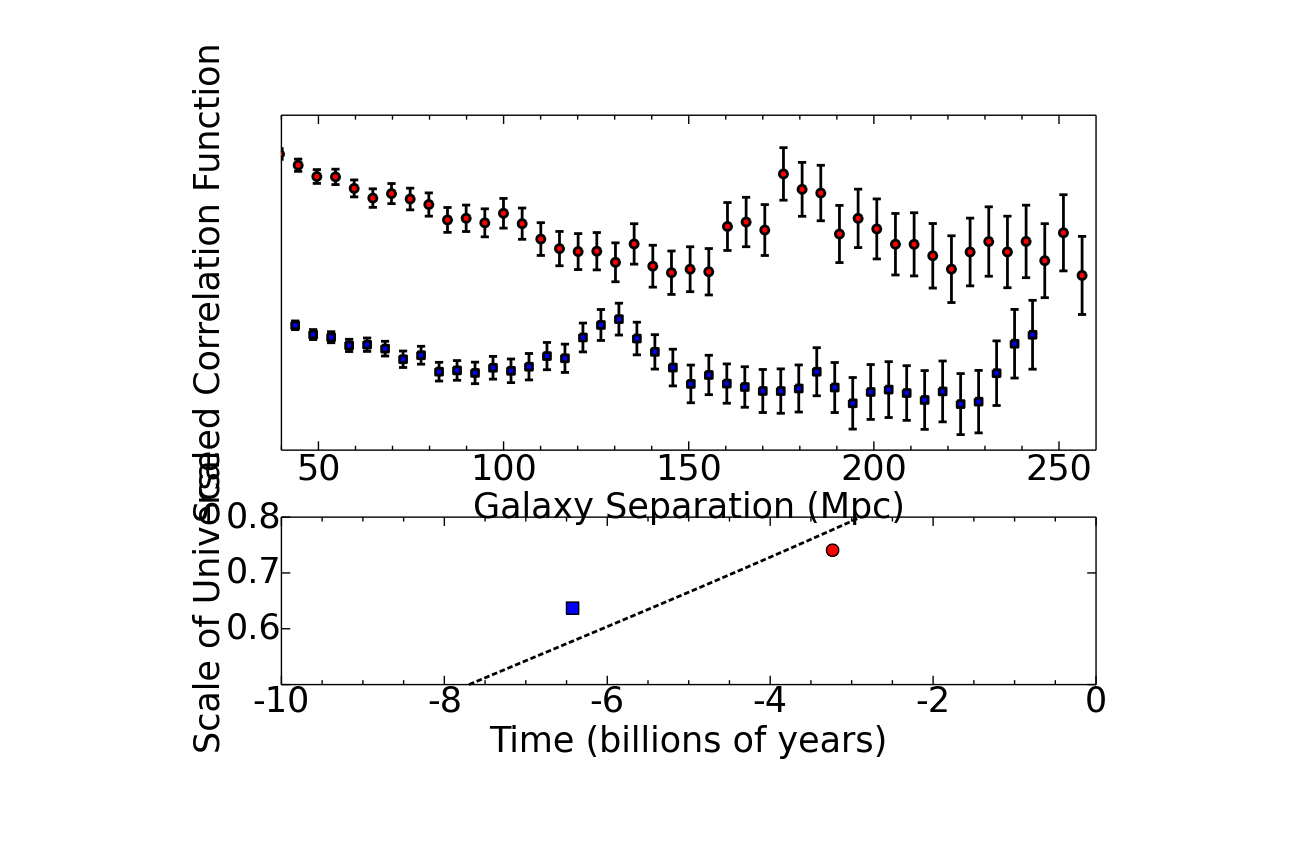

```mathematica
fig2[[1]]
```

```mathematica
Export["dr79_anim.gif", fig2, AnimationRepetitions->0, DisplayDurations->2.5];
```